Front edge velocity of ultra-intense circularly polarized laser pulses in a relativistically transparent plasma

https://iopscience.iop.org/article/10.1088/1361-6587/ab98e0
Notebook: Óscar Amaro, June 2021 @ GoLP-EPP
Contact: oscar.amaro@tecnico.ulisboa.pt

Introduction
In this notebook we reproduce results from the paper.

## Style

```mathematica
fntsz=20;
imgsz=300;
```

## Figure 2

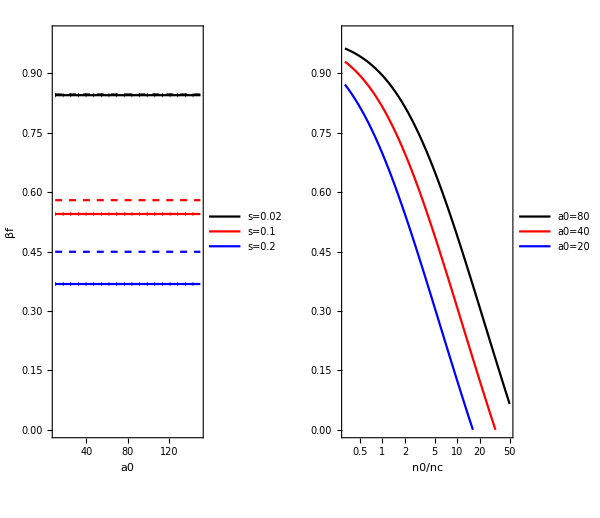

```mathematica
Clear[𝒦p,𝒦m,δ𝒦,s,βf,βf9,βf10,βf11,plta,pltb]
𝒦p=(8/(π^2 s)(Sqrt[1+8/(27 π^2 s)]+1))^(1/3);
𝒦m=(8/(π^2 s)(Sqrt[1+8/(27 π^2 s)]-1))^(1/3);
δ𝒦=𝒦p-𝒦m;
(* equation 10*)
βf10=δ𝒦-1;
(* equation 11 approximation *)
βf11=1/Sqrt[1+2π^2 s];
(* equation 9 *)
βf9[s_]:=NSolve[(1-βf)/(1+βf)^3==π^2/8 s,βf,Reals][[1,1,2]]

(* equation 10 is a very accurate *)
ListPlot[Table[{ss,1-((βf10/.{s->ss})/βf9[ss])},{ss,0.02,0.3,0.02}],Joined->True];

(* plot *)
(* line-eq 10, dash-eq 11, dots-eq 9 *)
plta=Plot[{βf10/.{s->0.02},βf10/.{s->0.1},βf10/.{s->0.2},βf11/.{s->0.02},βf11/.{s->0.1},βf11/.{s->0.2},βf9[0.02],βf9[0.1],βf9[0.2]},{a0,10,150},PlotRange->{{10,150},{0,1}},Frame->True,AspectRatio->2,PlotStyle->{Black,Red,Blue,Directive[Black,Dashed],Directive[Red,Dashed],Directive[Blue,Dashed],Directive[Black,Dotted,Thickness[0.02]],Directive[Red,Dotted,Thickness[0.02]],Directive[Blue,Dotted,Thickness[0.02]]},FrameLabel->{"a0","βf"},ImageSize->0.5imgsz,PlotLegends->Placed[{"s=0.02","s=0.1","s=0.2"},{0.5,0.2}]];
pltb=LogLinearPlot[{βf10//.{s->n0nc/a0,a0->80},βf10//.{s->n0nc/a0,a0->40},βf10//.{s->n0nc/a0,a0->20}},{n0nc,10^-0.5,10^1.7},PlotRange->{{10^-0.5,10^1.7},{0,1}},Frame->True,AspectRatio->2,PlotStyle->{Black,Red,Blue},FrameLabel->{"n0/nc",""},PlotLegends->Placed[{"a0=80","a0=40","a0=20"},{0.7,0.8}],ImageSize->0.5imgsz];
GraphicsRow[{plta,pltb},ImageSize->2imgsz]
```

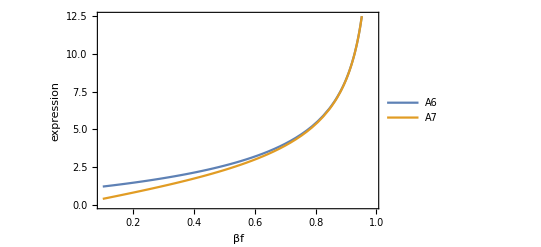

```mathematica
(* proof first term in A6 can be neglected *)
A6=(1-βf)^1.5/Sqrt[1+βf]+(4βf)/Sqrt[1-βf^2];
A7=(4βf)/Sqrt[1-βf^2];
Plot[{A6,A7},{βf,0.1,0.99},PlotLegends->{"A6","A7"},Frame->True,FrameLabel->{"βf","expression"}]
```

## Figure 3

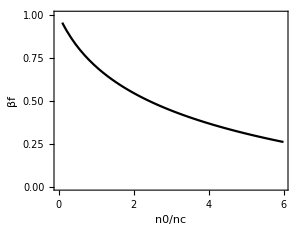

```mathematica
Clear[𝒦p,𝒦m,δ𝒦,s,βf,βf9,βf10,βf11]
𝒦p=(8/(π^2 s)(Sqrt[1+8/(27 π^2 s)]+1))^(1/3);
𝒦m=(8/(π^2 s)(Sqrt[1+8/(27 π^2 s)]-1))^(1/3);
δ𝒦=𝒦p-𝒦m;
(* equation 10*)
βf10=δ𝒦-1;

(* plot *)
Plot[{βf10//.{s->n0nc/a0,a0->20}},{n0nc,0.1,6},PlotRange->{{0,6},{0,1}},Frame->True,AspectRatio->3/4,PlotStyle->{Black},FrameLabel->{"n0/nc","βf"},ImageSize->imgsz]

(*ToDo: get green dashed line*)
```

## Figure 4

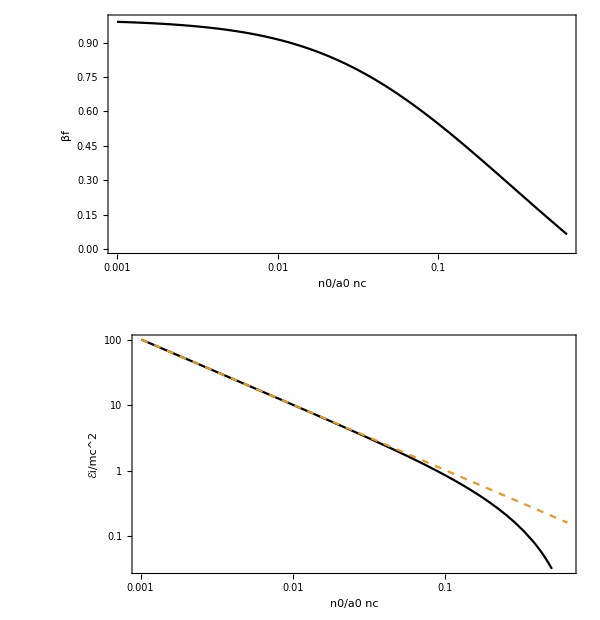

```mathematica
Clear[𝒦p,𝒦m,δ𝒦,s,βf,βf10,ℰi12,ℰi13,plta,pltb]
𝒦p=(8/(π^2 s)(Sqrt[1+8/(27 π^2 s)]+1))^(1/3);
𝒦m=(8/(π^2 s)(Sqrt[1+8/(27 π^2 s)]-1))^(1/3);
δ𝒦=𝒦p-𝒦m;
(* equation 10*)
βf10=δ𝒦-1;
(* equation 12 *)
ℰi12=1/δ𝒦+1/(2-δ𝒦)-2;
(* equation 13 approximation *)
ℰi13=1/(π^2 s);

(* plot *)
plta=LogLinearPlot[{βf10},{s,10^-3,10^-0.2},PlotRange->{{10^-3,10^-0.2},{0,1}},Frame->True,AspectRatio->1/2,PlotStyle->{Black},FrameLabel->{"n0/a0 nc","βf"},ImageSize->imgsz];
pltb=LogLogPlot[{ℰi12,ℰi13},{s,10^-3,10^-0.2},PlotRange->{{10^-3,10^-0.2},{10^-1.5,10^2}},Frame->True,AspectRatio->1/2,PlotStyle->{Black,Dashed},FrameLabel->{"n0/a0 nc","ℰi/mc^2"},ImageSize->imgsz];
GraphicsColumn[{plta,pltb},ImageSize->2imgsz]
```